## Extracting info from 1904.07265

### Neutrino mode - τ^- - extracting data

```mathematica
fig=Import["/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/Mathematica/Img_test_acompar.png","Image"];
```

```mathematica
imageData=ImageData[fig,DataReversed->True];
Manipulate[Graphics[{Raster[imageData,{{0,0},ImageDimensions[fig]}]},ImageSize->500],{{bottomLeft,{0,0}}},{{topRight,{300,300}}},{{bottomLeft,{0,0}},Locator},{{topRight,{300,300}},Locator}];
```

```mathematica
bottomLeft={50.5,54.};
topRight={757.,759.};

{xRange,yRange}={{0,20},{0,40}};

aspectRatio=1/Divide@@(topRight-bottomLeft);
scaling=Abs[Subtract@@xRange]*First@ImageDimensions[fig]/First@(topRight-bottomLeft);
```

Reconstructed energy

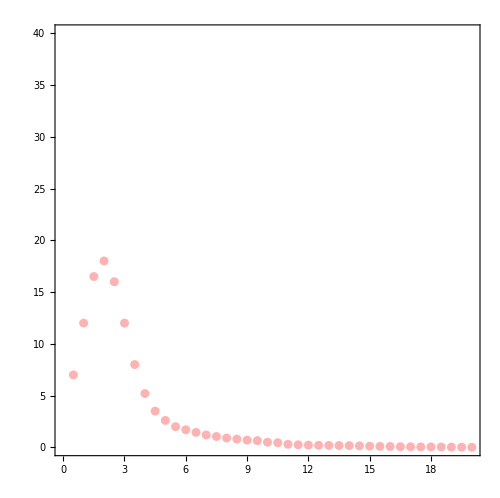

```mathematica
lis={7,12,16.5,18,16,12,8,5.2,3.5,2.6,2,1.7,1.45,1.2,1.05,0.9,0.8,0.7,0.65,0.5,0.45,0.3,0.25,0.22,0.2,0.19,0.18,0.17,0.15,0.12,0.1,0.09,.07,.06,.05,.045,.04,.03,.02,.01};
data=Table[{i*.5,lis[[i]]},{i,40}];Print["Reconstructed energy"]
ListPlot[data,{PlotRange->{xRange,yRange},PlotStyle->{{Red,Opacity[0.3]}},Prolog->{Inset[SetAlphaChannel[fig,.5],{xRange[[1]],yRange[[1]]},bottomLeft,scaling]},AxesOrigin->{0.05,1.5},AspectRatio->aspectRatio,Axes->False,ImageSize->500,Axes->True,ImagePadding->50,PlotRangeClipping->False,Frame->True}]
```

True energy

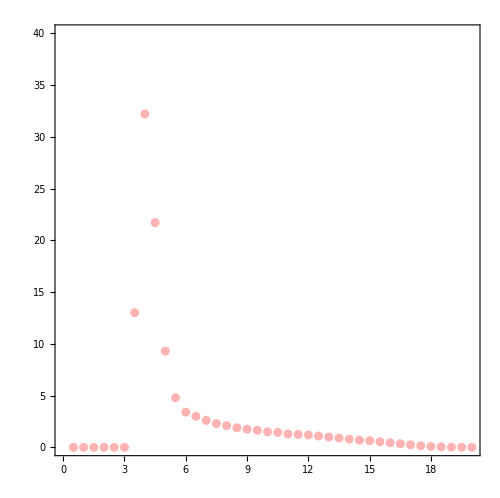

```mathematica
lis2={0,0,0,0,0,0,13.,32.2,21.7,9.3,4.8,3.4,3.,2.6,2.3,2.1,1.9,1.75,1.65,1.5,1.45,1.3,1.25,1.2,1.1,1.,.9,.8,.7,.65,.55,0.45,.35,.25,.15,.1,.05,.02,.01,.01};
data2=Table[{i*.5,lis2[[i]]},{i,40}];
Print["True energy"]
ListPlot[data2,{PlotRange->{xRange,yRange},PlotStyle->{{Red,Opacity[0.3]}},Prolog->{Inset[SetAlphaChannel[fig,.5],{xRange[[1]],yRange[[1]]},bottomLeft,scaling]},AxesOrigin->{0.05,1.5},AspectRatio->aspectRatio,Axes->False,ImageSize->500,Axes->True,ImagePadding->50,PlotRangeClipping->False,Frame->True}]
```

### Transformation function

```mathematica
Clear[f]
f[Ere_,Etrue_]:=(*1/σe*)Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}]
```

```mathematica
dataN=Table[Maximize[f[i*.5,x],x][[2,1,2]],{i,40}]
```

{1.11111,2.22222,3.33333,4.44444,5.55556,6.66667,7.77778,8.88889,10.,11.1111,12.2222,13.3333,14.4444,15.5556,16.6667,17.7778,18.8889,20.,21.1111,22.2222,23.3333,24.4444,25.5556,26.6667,27.7778,28.8889,30.,31.1111,32.2222,33.3333,34.4444,35.5556,36.6667,37.7778,38.8889,40.,41.1111,42.2222,43.3333,44.4444}

```mathematica
figN=Import["/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/Mathematica/Img_test_MappingTrueReco.png","Image"];
```

```mathematica
imageData=ImageData[figN,DataReversed->True];
Manipulate[Graphics[{Raster[imageData,{{0,0},ImageDimensions[fig]}]},ImageSize->500],{{bottomLeft,{0,0}}},{{topRight,{300,300}}},{{bottomLeft,{0,0}},Locator},{{topRight,{300,300}},Locator}];
```

```mathematica
bottomLeft={42.,51.};
topRight={1.01*755.5,0.975*766.};

{xRange,yRange}={{0,20},{0,20}};

aspectRatio=1/Divide@@(topRight-bottomLeft);
scaling=Abs[Subtract@@xRange]*First@ImageDimensions[fig]/First@(topRight-bottomLeft)
```

21.5518

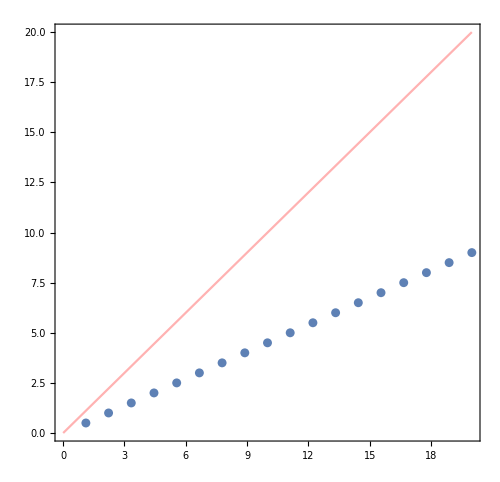

```mathematica
Show[Plot[x,{x,0,20},{PlotRange->{xRange,yRange},PlotStyle->{{Red,Opacity[0.3]}},Prolog->{Inset[SetAlphaChannel[figN,.5],{xRange[[1]],yRange[[1]]},bottomLeft,scaling]},AxesOrigin->{0.05,1.5},AspectRatio->aspectRatio,Axes->False,ImageSize->500,Axes->True,ImagePadding->50,PlotRangeClipping->False,Frame->True}],ListPlot@Transpose[{dataN,data[[All,1]]}],Frame->True]
```

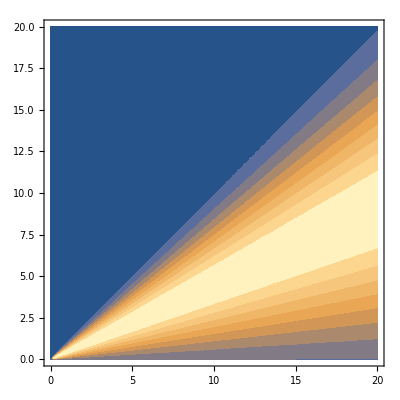

```mathematica
ContourPlot[f[ere,etrue],{etrue,0,20},{ere,0,20},ContourLines->False]
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.4,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.4,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0.5,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{.5*j,Sum[fn[0.5*j,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,0.5,20}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,0.5,20}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,0.5,20}]
fac2=ndtrue/ndreInt
dataT=Table[{.5*j,fac2*Sum[fn[0.5*j,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;
```

56.7425

55.6621

56.7326

1.00018

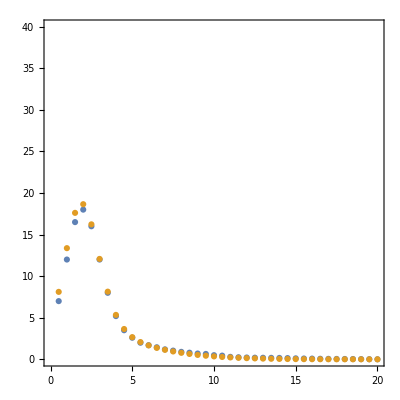

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```